General::munfl: (-0.00103946)^104 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.00103946)^112 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.00103946)^120 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

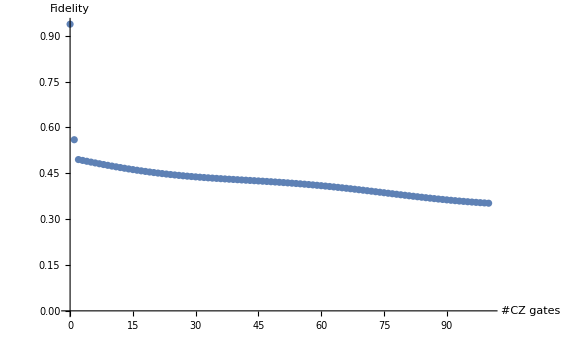

```mathematica
x=1/16 (4+(ⅇ^(-8 ⅈ (ϵ+η)) Subscript[d, 1]^4)^n+(ⅇ^(8 ⅈ (ϵ+η)) Subscript[d, 1]^4)^n+(ⅇ^(-8 ⅈ (η+κ)) Subscript[d, 2]^4)^n+(ⅇ^(8 ⅈ (η+κ)) Subscript[d, 2]^4)^n+(ⅇ^(-8 ⅈ (ϵ-κ)) Subscript[d, 1]^4 Subscript[d, 2]^4)^n+(ⅇ^(8 ⅈ (ϵ-κ)) Subscript[d, 1]^4 Subscript[d, 2]^4)^n+(ⅇ^(-8 ⅈ (ϵ+κ)) Subscript[d, 1]^4 Subscript[d, 2]^4)^n+(ⅇ^(8 ⅈ (ϵ+κ)) Subscript[d, 1]^4 Subscript[d, 2]^4)^n-(-1+Subscript[r, 1])^(4 n)+(ⅇ^(-8 ⅈ (η-κ)) Subscript[d, 2]^4 (-1+Subscript[r, 1])^4)^n+(ⅇ^(8 ⅈ (η-κ)) Subscript[d, 2]^4 (-1+Subscript[r, 1])^4)^n-(((ⅇ^(8 ⅈ (η+κ)) Subscript[d, 2]^4)^n-(ⅇ^(-8 ⅈ (η-κ)) Subscript[d, 2]^4 (-1+Subscript[r, 1])^4)^n) Subscript[r, 1])/(1+ⅇ^(4 ⅈ η)-Subscript[r, 1])+(ⅇ^(4 ⅈ η) ((ⅇ^(-8 ⅈ (η+κ)) Subscript[d, 2]^4)^n-(ⅇ^(8 ⅈ (η-κ)) Subscript[d, 2]^4 (-1+Subscript[r, 1])^4)^n) Subscript[r, 1])/(-1-ⅇ^(4 ⅈ η)+ⅇ^(4 ⅈ η) Subscript[r, 1])-(-1+Subscript[r, 1])^(4 n) (-1+(-1+Subscript[r, 2])^(4 n))+(ⅇ^(-8 ⅈ (ϵ-η)) Subscript[d, 1]^4 (-1+Subscript[r, 2])^4)^n+(ⅇ^(8 ⅈ (ϵ-η)) Subscript[d, 1]^4 (-1+Subscript[r, 2])^4)^n+((-1+Subscript[r, 1])^4 (-1+Subscript[r, 2])^4)^n+1/(-1-ⅇ^(4 ⅈ η)+ⅇ^(4 ⅈ η) Subscript[r, 2])ⅇ^(-4 ⅈ (2 ϵ+η)) Subscript[r, 2] (Subscript[d, 1]^4 UnitStep[1-n]+Subscript[d, 1]^4 (ⅇ^(-8 ⅈ (ϵ+η)) Subscript[d, 1]^4)^(-1+n) UnitStep[-2+n]-ⅇ^(8 ⅈ (ϵ+η)) (ⅇ^(-8 ⅈ (ϵ-η)) Subscript[d, 1]^4 (-1+Subscript[r, 2])^4)^n UnitStep[-2+n])+1/(1+ⅇ^(4 ⅈ η)-Subscript[r, 2])ⅇ^(-8 ⅈ η) Subscript[r, 2] (ⅇ^(8 ⅈ ϵ) Subscript[d, 1]^4 (-1+Subscript[r, 2])^4 UnitStep[1-n]-ⅇ^(8 ⅈ (η+n (ϵ+η))) Subscript[d, 1]^(4 n) UnitStep[-2+n]+ⅇ^(8 ⅈ η) (ⅇ^(8 ⅈ (ϵ-η)) Subscript[d, 1]^4 (-1+Subscript[r, 2])^4)^n UnitStep[-2+n]))/.{κ->π/4,ϵ->π/4}/.{Subscript[d, i_]->Exp[-tg/Subscript[T, i,2]],Subscript[r, i_]->Exp[-tg/Subscript[T, i,1]]}/.{tg->104,Subscript[T, 1,1]->100000,Subscript[T, 1,2]->100000,Subscript[T, 2,1]->100000,Subscript[T, 2,2]->100000};
data=Table[{i,Abs[(x/.{η->0.01,n->i})]},{i,0,100}];
ListPlot[data,PlotRange->All,AxesLabel->{"#CZ gates", "Fidelity"}]
```

Match IBM result with overrotated X and CZ gate.

# MIT Results

## Load data